# Parallelized ACQE Two-qubit random Hamiltonian

## 1. Hamiltonian

```mathematica
AllPauli=Array[KroneckerProduct[PauliMatrix[#1],PauliMatrix[#2]]&,{4,4}];
(*RR=RandomReal[{-2,2},{4,4}];*)
RR={{-1.0105625030082592,1.5053289046071434,-0.899202784680913,-1.8000703619021232},{0.6099777471405252,-0.589742421383419,-1.1047548993460294,1.5818920178733826},{-1.2472464784658674,-0.9894046091041471,1.9312934292491963,-0.12853037184241956},{-0.5033199986178252,-0.1200376788827473,0.9547049992732353,1.520460248592677}};(*The numbers of the calculation in the paper*)
Aux=AllPauli*RR;
Ham=ConstantArray[0,{4,4}];
For[i=1,i<=4,i++,For[j=1,j<=4,j++,Ham+=Aux[[i,j]]]]
Ham = Re[Ham];
MatrixForm[Ham]
Eigenvalues[Ham]
```

(4.27793 | -1.75057 | -2.69927 | -0.42082
-1.75057 | -1.49407 | -1.6003 | -0.900868
-2.69927 | -1.6003 | 0.672402 | 0.743926
-0.42082 | -0.900868 | 0.743926 | 2.62558)

{5.92925,-3.47137,3.03936,0.584601}

## 2. Antisymmetric operators

```mathematica
Ladder={{{1,0},{0,0}},{{0,0},{0,1}}};
A=ConstantArray[0,{6,4,4}];
A[[1]]=KroneckerProduct[I PauliMatrix[2],Ladder[[1]]];
A[[2]]=KroneckerProduct[I PauliMatrix[2],Ladder[[2]]];
A[[3]]=KroneckerProduct[Ladder[[1]],I PauliMatrix[2]];
A[[4]]=KroneckerProduct[Ladder[[2]],I PauliMatrix[2]];
A[[5]][[2,3]]=1;A[[5]][[3,2]]=-1;
A[[6]][[1,4]]=1;A[[6]][[4,1]]=-1;
Commut[A_,B_]:=A .B - B. A;
Expect[ve1_,AA_]:=Conjugate[ve1].AA.ve1;
vv=ConstantArray[0,{4,4}];
w={0.4,0.3,0.2,0.1};
```

## 3. Algorithm

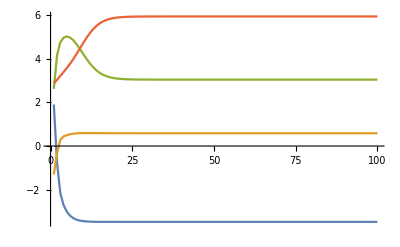

```mathematica
Ene=ConstantArray[0,{100,4}];
Vec=ConstantArray[0,{101,4,4}];
Pro=ConstantArray[0,{100,4}];
v=ConstantArray[0,{4,4}];
v[[1]]={1,0,0,0};v[[2]]={0,1,0,0};v[[3]]={0,0,1,0};v[[4]]={0,0,0,1};
Vec[[1,1]]=v[[1]];Vec[[1,2]]=v[[2]];Vec[[1,3]]=v[[3]];Vec[[1,4]]=v[[4]];
eta=0.29;
For[m=1,m<=100,m++,grad =ConstantArray[0,6];
vv=ConstantArray[0,{4,4}];
For[i=1,i<=6,i++,For[j=1,j<=4,j++,grad[[i]] += w[[j]]*Expect[v[[j]],Commut[A[[i]],Ham]]]];
B=ConstantArray[0,{4,4}];
For[i=1,i<=6,i++,B += grad[[i]]*A[[i]]];
For[i=1,i<=4,i++,vv[[i]] = MatrixExp[eta B].v[[i]];Vec[[m+1,i]]=vv[[i]];Ene[[m,i]]=Chop[Expect[vv[[i]],Ham]]];
v=vv]
ListPlot[{Ene[[All,1]],Ene[[All,2]],Ene[[All,3]],Ene[[All,4]]},Joined->True]
```

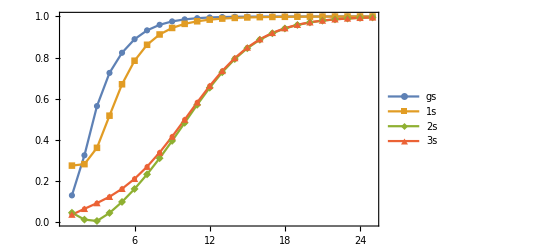

```mathematica
Num1=25;
BB=Ordering[Ene[[100]]];
BB1=Ordering[Eigenvalues[Ham]];
Pro=ConstantArray[0,{Num1,4}];
For[m=1,m<=Num1,m++,For[j=1,j<=4,j++,Pro[[m,j]]=(Vec[[m,BB[[j]]]].Eigenvectors[Ham][[BB1[[j]]]])^2]]
ListPlot[{Pro[[All,1]],Pro[[All,2]],Pro[[All,3]],Pro[[All,4]]},PlotRange->All,Joined->True,TicksStyle->Directive[45],AxesStyle->Directive[Black,28],Mesh->All, Frame->True,PlotMarkers->Automatic,BaseStyle->{FontSize->14},PlotLegends->Placed[{"gs","1s","2s","3s"},{0.8,0.4}]]
```

```mathematica
Export["out2.dat",Pro];
```

```mathematica
FilePrint["out2.dat"]
```

0.12902141674510983	0.27395828459823524	0.04463951377711083	0.03538853636965104
0.3241162313009245	0.28113097397875003	0.01120518139476153	0.06352105400131995
0.5636555929691782	0.3606148633614514	0.0044755801973237795	0.09151918802595671
0.7252391165513781	0.51707176480401	0.04338931551414877	0.12226063369978876
0.8233607337777697	0.6699153721551032	0.09722519130389809	0.16105874542568593
0.8892199914192807	0.7845307694577407	0.160375468168468	0.20962439531278643
0.932321782741528	0.8621516093441314	0.23151423858339612	0.26859701256507357
0.9593817443065049	0.9123233825349006	0.3099341031978225	0.3376245926574159
0.9758899059068711	0.9440571724812142	0.39439370325629336	0.4150538160372137
0.9857827741115841	0.9639856407117453	0.48236800203603236	0.49780751503350434
0.9916483620997528	0.976526590657922	0.5701193549886605	0.5816739654537477
0.9951045762517523	0.9844830292896969	0.6533989068345024	0.6620479319965865
0.9971338945844401	0.9895919427961368	0.7284243490776409	0.7348912564743879
0.998323056017245	0.9929196360049956	0.7926863697038826	0.797511804157096
0.9990191447290332	0.9951204241822125	0.845262934418487	0.8488546341807914
0.9994263782787433	0.996598160070153	0.8866205610989509	0.8892873365066716
0.9996645559879123	0.997604698720754	0.9181251767547022	0.9201008286071319
0.9998038409505341	0.9982992406351118	0.9415274730468532	0.9429884285568583
0.9998852903649638	0.9987839863576928	0.9585822459730485	0.9596610348309289
0.9999329191697157	0.9991256243330636	0.970836809482422	0.9716325296353481
0.9999607712192138	0.9993683834920969	0.9795524957553736	0.9801389480652233
0.9999770586712835	0.9995420543602257	0.985706098089141	0.9861380642391774
0.999986583516694	0.9996669890416949	0.9900284188912414	0.9903464602156743
0.9999921537152904	0.9997572681698835	0.9930535234202503	0.993287615693891
0.9999954112582806	0.9998227408052803	0.9951654665638128	0.9953377321130489